```mathematica
delta={2.44,2.54,2.64,2.74,2.84,2.94,3.04,3.14,3.24,3.34,3.44,3.54,3.64};
```

```mathematica
gap={1.2783,1.3180,1.3581,1.3987,1.4396,1.4809,1.5227,1.5648,1.6073,1.6502,1.6935,1.7371,1.7812};
```

```mathematica
gapvsdelta=Table[{delta[[i]],gap[[i]]},{i,1,13}];
```

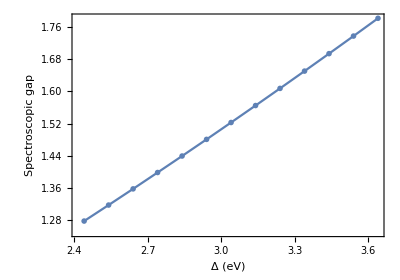

```mathematica
figgapvsdelta=ListPlot[gapvsdelta,PlotMarkers->{"OpenMarkers",8},PlotRange->Automatic,PlotStyle->Automatic,(*PlotLegends->Placed[LineLegend[{"T=0.02eV"},LabelStyle->{14},LegendLayout->{"Row",2}],{0.8,0.15}],*)Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"Δ (eV)","Spectroscopic gap"},Joined->True]
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_correlation/figgapvsdelta.pdf",figgapvsdelta,"PDF"];
```

```mathematica
k=(1.3180-1.2783)/(0.1)
```

0.397

```mathematica
y[x_]=k*x+0.31;
```

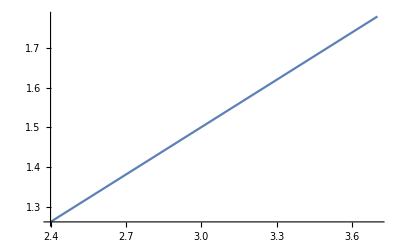

```mathematica
A=Plot[y[x],{x,2.4,3.7}]
```

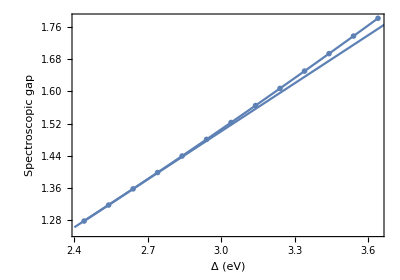

```mathematica
Show[figgapvsdelta,A]
```

```mathematica
lm=LinearModelFit[gapvsdelta,x,x]
```

FittedModel[0.251238+0.419137 x]

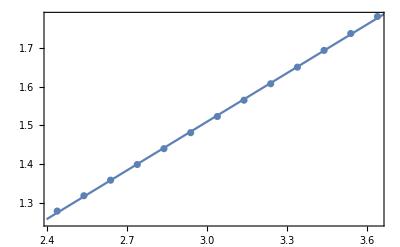

```mathematica
Show[ListPlot[gapvsdelta],Plot[lm[x],{x,2.4,3.7}],Frame->True]
```